```mathematica
Directory[]
```

/home/cooper-cooper

```mathematica
SetDirectory["/home/cooper-cooper/Desktop/vans/results/xxz/plot"]
```

/home/cooper-cooper/Desktop/vans/results/xxz/plot

1

Eigenvalues::arh: Because finding 16384 out of the 16384 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

2

Eigenvalues::arh: Because finding 16384 out of the 16384 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

3

Eigenvalues::arh: Because finding 16384 out of the 16384 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

General::stop: Further output of Eigenvalues::arh will be suppressed during this calculation.

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

xxz14.csv

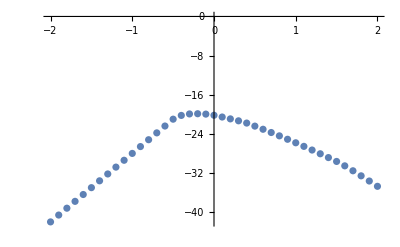

```mathematica
g=1.0;op[n_Integer,k_Integer,a_?MatrixQ]/;1≤k≤n&&Dimensions[a]=={2,2}:=KroneckerProduct[IdentityMatrix[2^(k-1),SparseArray],a,IdentityMatrix[2^(n-k),SparseArray]];
sz[n_Integer,k_Integer]/;1≤k≤n:=op[n,k,PauliMatrix[3]];
sy[n_Integer,k_Integer]/;1≤k≤n:=op[n,k,PauliMatrix[2]];
sx[n_Integer,k_Integer]/;1≤k≤n:=op[n,k,PauliMatrix[1]];
HH[n_Integer/;n≥3,g_,J_]:=g*Sum[sz[n,k],{k,n}]+Sum[sx[n,k].sx[n,Mod[k+1,n,1]],{k,n}] + Sum[sy[n,k].sy[n,Mod[k+1,n,1]],{k,n}] + J*Sum[sz[n,k].sz[n,Mod[k+1,n,1]],{k,n}];
js=Table[k,{k,-2,2,.1}];
num =Table[Print[k];J=js[[k]];kk=HH[14,1.0,J]//Eigenvalues//Min;{J,kk},{k,1,Length[js]}];
Export["xxz14.csv",num]
ListPlot[num, PlotRange->All]
```

```mathematica
g=1.0;op[n_Integer,k_Integer,a_?MatrixQ]/;1≤k≤n&&Dimensions[a]=={2,2}:=KroneckerProduct[IdentityMatrix[2^(k-1),SparseArray],a,IdentityMatrix[2^(n-k),SparseArray]];
sz[n_Integer,k_Integer]/;1≤k≤n:=op[n,k,PauliMatrix[3]];
sy[n_Integer,k_Integer]/;1≤k≤n:=op[n,k,PauliMatrix[2]];
sx[n_Integer,k_Integer]/;1≤k≤n:=op[n,k,PauliMatrix[1]];
HH[n_Integer/;n≥3,g_,J_]:=g*Sum[sz[n,k],{k,n}]+Sum[sx[n,k].sx[n,Mod[k+1,n,1]],{k,n}] + Sum[sy[n,k].sy[n,Mod[k+1,n,1]],{k,n}] + J*Sum[sz[n,k].sz[n,Mod[k+1,n,1]],{k,n}];
js=Table[k,{k,-2,2,.1}];
num =Table[Print[k];J=js[[k]];kk=HH[14,1.0,J]//Eigenvalues;kk=kk[[1;;10]];{J,kk},{k,1,Length[js]}];
Export["xxz10first_14.csv",num]
```

1

Eigenvalues::arh: Because finding 16384 out of the 16384 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

2

Eigenvalues::arh: Because finding 16384 out of the 16384 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

3

Eigenvalues::arh: Because finding 16384 out of the 16384 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

General::stop: Further output of Eigenvalues::arh will be suppressed during this calculation.

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

```mathematica
g=1.0;op[n_Integer,k_Integer,a_?MatrixQ]/;1≤k≤n&&Dimensions[a]=={2,2}:=KroneckerProduct[IdentityMatrix[2^(k-1),SparseArray],a,IdentityMatrix[2^(n-k),SparseArray]];
sz[n_Integer,k_Integer]/;1≤k≤n:=op[n,k,PauliMatrix[3]];
sy[n_Integer,k_Integer]/;1≤k≤n:=op[n,k,PauliMatrix[2]];
sx[n_Integer,k_Integer]/;1≤k≤n:=op[n,k,PauliMatrix[1]];
HH[n_Integer/;n≥3,g_,J_]:=g*Sum[sz[n,k],{k,n}]+Sum[sx[n,k].sx[n,Mod[k+1,n,1]],{k,n}] + Sum[sy[n,k].sy[n,Mod[k+1,n,1]],{k,n}] + J*Sum[sz[n,k].sz[n,Mod[k+1,n,1]],{k,n}];
js=Table[k,{k,-3,5.1,.1}];
num =Table[Print[k];J=js[[k]];kk=HH[8,1.0,J]//Eigenvalues//Sort;kk=kk[[1;;10]];kk,{k,1,Length[js]}];
Export["~/Desktop/vans/8qubitsxxzpaper.csv",num]
```

1

Eigenvalues::arh: Because finding 256 out of the 256 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

2

Eigenvalues::arh: Because finding 256 out of the 256 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

3

Eigenvalues::arh: Because finding 256 out of the 256 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

General::stop: Further output of Eigenvalues::arh will be suppressed during this calculation.

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

~/Desktop/vans/8qubitsxxzpaper.csv

```mathematica
Export["8qubitsxxzpaper.csv",num]
```

8qubitsxxzpaper.csv

```mathematica
num
```

{{-15.0195,-14.7157,14.2616,14.0437,-13.8209,13.6666,13.2,-13.1815,-12.7192,-12.7192},{-15.3959,-14.8476,-14.2877,14.2655,14.1715,13.8,13.3714,-13.0633,-13.0633,13.0361},{-15.7858,-14.9854,-14.7728,14.4912,14.4,14.0932,14.,13.6361,13.6361,-13.4666},{-16.1885,-15.2761,-15.1284,15.,15.,14.7215,14.2361,14.2361,14.0284,-13.8855},{-16.6032,16.,-15.7974,15.6,-15.2759,14.9577,14.8361,14.8361,-14.3188,-14.3188},{-17.0293,17.,-16.3366,16.2,15.4361,15.4361,-15.4277,15.2014,-14.7653,-14.7653},{18.,-17.466,-16.8937,16.8,16.0361,16.0361,-15.5831,15.4546,-15.2239,-15.2239},{19.,-17.9127,-17.4688,17.4,16.6361,16.6361,-15.7419,15.7198,-15.6935,-15.6935},{20.,-18.3688,-18.0618,18.,17.2361,17.2361,-16.3688,-16.1731,-16.1731,16.},{21.,-18.8337,-18.6729,18.6,17.8361,17.8361,-17.0938,-16.6618,-16.6618,16.2987},{22.,-19.3067,-19.3022,19.2,18.4361,18.4361,-17.8364,-17.1588,-17.1588,16.6191},{23.,-19.9497,19.8,-19.7874,19.0361,19.0361,-18.5952,-17.6633,-17.6633,17.0361},{24.,-20.6154,20.4,-20.2752,19.6361,19.6361,-19.369,-18.1745,-18.1745,17.6361},{25.,-21.2992,21.,-20.7696,20.2361,20.2361,-20.1566,-18.692,-18.692,18.2361},{26.,-22.0009,21.6,-21.2701,-20.9571,20.8361,20.8361,-19.215,-19.215,18.8361},{27.,-22.7201,22.2,-21.7764,-21.7696,21.4361,21.4361,-19.7431,-19.7431,19.4361},{28.,-23.4565,22.8,-22.5931,-22.2881,22.0361,22.0361,-20.2759,-20.2759,20.0361},{29.,-24.2095,-23.427,23.4,-22.8047,22.6361,22.6361,-20.813,-20.813,20.6361},{30.,-24.9783,-24.2704,24.,-23.3259,23.2361,23.2361,-21.3539,-21.3539,21.2361}}

{{-15.0195,-14.7157,-13.8209,-13.1815,-12.7192,-12.7192,-12.6769,-12.6769,-12.5491,-12.5491},{-15.3959,-14.8476,-14.2877,-13.0633,-13.0633,-12.9703,-12.8549,-12.8549,-12.6771,-12.6771},{-15.7858,-14.9854,-14.7728,-13.4666,-13.4666,-12.9973,-12.9973,-12.9543,-12.9543,-12.7603},{-16.1885,-15.2761,-15.1284,-13.8855,-13.8855,-13.2496,-13.2496,-13.1455,-13.1455,-13.0651},{-16.6032,-15.7974,-15.2759,-14.3188,-14.3188,-13.6767,-13.5627,-13.5627,-13.2988,-13.2988},{-17.0293,-16.3366,-15.4277,-14.7653,-14.7653,-14.315,-13.8933,-13.8933,-13.6041,-13.4564},{-17.466,-16.8937,-15.5831,-15.2239,-15.2239,-14.9777,-14.2408,-14.2408,-14.0898,-13.6179},{-17.9127,-17.4688,-15.7419,-15.6935,-15.6935,-15.6629,-14.6047,-14.6047,-14.5828,-13.9127},{-18.3688,-18.0618,-16.3688,-16.1731,-16.1731,-15.9037,-15.0824,-14.9847,-14.9847,-14.3688},{-18.8337,-18.6729,-17.0938,-16.6618,-16.6618,-16.0683,-15.5881,-15.3799,-15.3799,-14.8337},{-19.3067,-19.3022,-17.8364,-17.1588,-17.1588,-16.2353,-16.0995,-15.7897,-15.7897,-15.3067},{-19.9497,-19.7874,-18.5952,-17.6633,-17.6633,-16.6161,-16.4045,-16.2133,-16.2133,-15.7874},{-20.6154,-20.2752,-19.369,-18.1745,-18.1745,-17.1375,-16.6499,-16.6499,-16.5757,-16.2752},{-21.2992,-20.7696,-20.1566,-18.692,-18.692,-17.6634,-17.0986,-17.0986,-16.7696,-16.7488},{-22.0009,-21.2701,-20.9571,-19.215,-19.215,-18.1934,-17.5587,-17.5587,-17.2701,-17.0969},{-22.7201,-21.7764,-21.7696,-19.7431,-19.7431,-18.7273,-18.0292,-18.0292,-17.7764,-17.6453},{-23.4565,-22.5931,-22.2881,-20.2759,-20.2759,-19.2648,-18.5094,-18.5094,-18.2881,-18.1971},{-24.2095,-23.427,-22.8047,-20.813,-20.813,-19.8055,-18.9984,-18.9984,-18.8047,-18.752},{-24.9783,-24.2704,-23.3259,-21.3539,-21.3539,-20.3494,-19.4956,-19.4956,-19.3259,-19.3096}}

```mathematica
num
```

{{0.2,{-15.0195,-14.7157,-13.8209,-13.1815,-12.7192,-12.7192,-12.6769,-12.6769,-12.5491,-12.5491}},{0.3,{-15.3959,-14.8476,-14.2877,-13.0633,-13.0633,-12.9703,-12.8549,-12.8549,-12.6771,-12.6771}},{0.4,{-15.7858,-14.9854,-14.7728,-13.4666,-13.4666,-12.9973,-12.9973,-12.9543,-12.9543,-12.7603}},{0.5,{-16.1885,-15.2761,-15.1284,-13.8855,-13.8855,-13.2496,-13.2496,-13.1455,-13.1455,-13.0651}},{0.6,{-16.6032,-15.7974,-15.2759,-14.3188,-14.3188,-13.6767,-13.5627,-13.5627,-13.2988,-13.2988}},{0.7,{-17.0293,-16.3366,-15.4277,-14.7653,-14.7653,-14.315,-13.8933,-13.8933,-13.6041,-13.4564}},{0.8,{-17.466,-16.8937,-15.5831,-15.2239,-15.2239,-14.9777,-14.2408,-14.2408,-14.0898,-13.6179}},{0.9,{-17.9127,-17.4688,-15.7419,-15.6935,-15.6935,-15.6629,-14.6047,-14.6047,-14.5828,-13.9127}},{1.,{-18.3688,-18.0618,-16.3688,-16.1731,-16.1731,-15.9037,-15.0824,-14.9847,-14.9847,-14.3688}},{1.1,{-18.8337,-18.6729,-17.0938,-16.6618,-16.6618,-16.0683,-15.5881,-15.3799,-15.3799,-14.8337}},{1.2,{-19.3067,-19.3022,-17.8364,-17.1588,-17.1588,-16.2353,-16.0995,-15.7897,-15.7897,-15.3067}},{1.3,{-19.9497,-19.7874,-18.5952,-17.6633,-17.6633,-16.6161,-16.4045,-16.2133,-16.2133,-15.7874}},{1.4,{-20.6154,-20.2752,-19.369,-18.1745,-18.1745,-17.1375,-16.6499,-16.6499,-16.5757,-16.2752}},{1.5,{-21.2992,-20.7696,-20.1566,-18.692,-18.692,-17.6634,-17.0986,-17.0986,-16.7696,-16.7488}},{1.6,{-22.0009,-21.2701,-20.9571,-19.215,-19.215,-18.1934,-17.5587,-17.5587,-17.2701,-17.0969}},{1.7,{-22.7201,-21.7764,-21.7696,-19.7431,-19.7431,-18.7273,-18.0292,-18.0292,-17.7764,-17.6453}},{1.8,{-23.4565,-22.5931,-22.2881,-20.2759,-20.2759,-19.2648,-18.5094,-18.5094,-18.2881,-18.1971}},{1.9,{-24.2095,-23.427,-22.8047,-20.813,-20.813,-19.8055,-18.9984,-18.9984,-18.8047,-18.752}},{2.,{-24.9783,-24.2704,-23.3259,-21.3539,-21.3539,-20.3494,-19.4956,-19.4956,-19.3259,-19.3096}}}

```mathematica
Table[num[[k]][[2]], {k,Length[num]}]
```

{-11.6569,-11.9037,-12.161,-12.4279,-12.7037,-12.9879,-13.2798,-13.5789,-13.8845,-14.1963,-14.6044,-15.0983,-15.6063,-16.1284,-16.6644,-17.2142,-17.7774,-18.3538,-18.9429,-19.5444,-20.1577,-20.7823,-21.4177,-22.0632,-22.7183,-23.3823,-24.0548,-24.7352,-25.4228,-26.1173,-26.8181}

```mathematica
{-11.6569,-11.4221,-11.4572,-11.4969,-11.6,-12.,-12.8,-13.6,-14.4,-15.2,-16.,-16.8,-17.6,-18.4,-19.2,-20.,-20.8,-21.6,-22.4,-23.2,-24.,-24.8,-25.6,-26.4,-27.2,-28.,-28.8,-29.6,-30.4,-31.2,-32.}
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.}

{-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.}

```mathematica
Length[js]
```

20